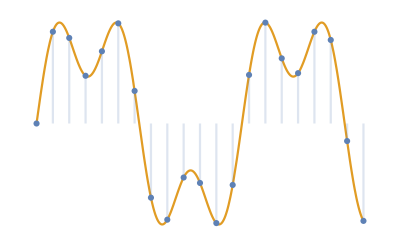

```mathematica
Show[
Plot[{, Sin[x]+1/2 Sin[3x]},{x,0,10},Axes->False],
DiscretePlot[ Sin[x]+1/2 Sin[3x],{x,0,10,.5}]
]
```

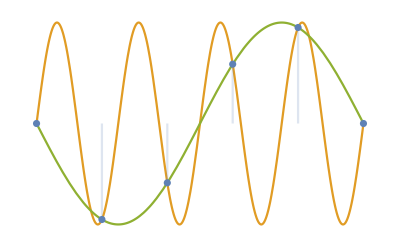

```mathematica
points=Table[Sin[.8 2π x],{x,5}];
fit=FindFit[points,A1 Sin[ω1 x+ϕ1]+A2 Sin[ω2 x+ϕ2],{A1,ω1,ϕ1,A2,ω2,ϕ2},x];
fitFn[x_]:=A1 Sin[ω1 x+ϕ1]+A2 Sin[ω2 x+ϕ2] /.fit

Show[
Plot[{, Sin[.8 2π x],fitFn[x]},{x,0,5},Axes->False],
DiscretePlot[ Sin[.8 2π x],{x,0,5,1}]
]
```

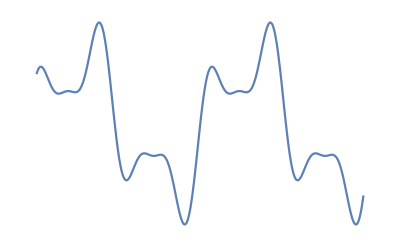

```mathematica
Plot[Sin[x]+2/3 Sin[3x+1]+1/4 Sin[5x+2],{x,0,12},Axes->False]
```

```mathematica
points=N[#,4]&/@Table[Sin[x]+2/3 Sin[3x+1]+1/4 Sin[5x+2],{x,0,2π,(2π)/300}];

dft=Fourier[points];
```

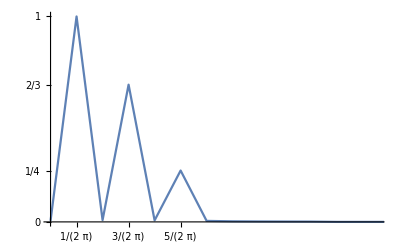

```mathematica
ListLinePlot[Transpose[{
Range[0, (1/(2 π/300)), 1/(2 π/300)/(Length[dft] - 1)],
 Abs[dft]/Max[Abs[dft]]
}]
,PlotRange->{{0,2},All},
Ticks->{{1/(2π),3/(2π),5/(2π)},{1,2/3,1/4,0}},
GridLines->{{1/(2π),3/(2π),5/(2π)},{1,2/3,1/4}},
AxesStyle->White,
GridLinesStyle->Thick]
```